## Moments of Inertia

```mathematica
ClearAll["Global`*"]
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->22};
```

```mathematica
betaExp=0.38;
gammaExp=20;
gamma=22; (* from the fitting procedure of W2 formalism *)
```

```mathematica
moisW2={72,15,7};
```

```mathematica
rigidMOI[I0_,k_,beta_,gamma_]:=I0*(1-beta*Sqrt[5/(4π)]Cos[gamma*π/180-2/3 π*k]);
hydroMOI[I0_,k_,gamma_]:=4/3*I0*Sin[gamma*π/180-2/3 π*k]^2;
```

```mathematica
I0rig=Values@NSolve[rigidMOI[a,1,betaExp,gamma]==moisW2[[1]]][[1,1]];
I0hyd=Values@NSolve[hydroMOI[a,1,gamma]==moisW2[[1]]][[1,1]];
```

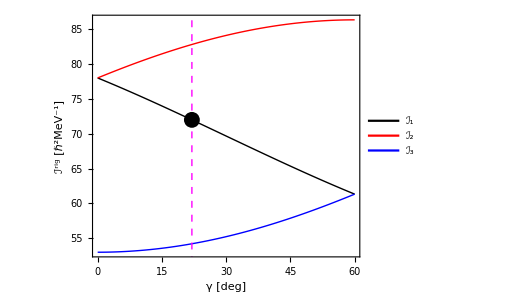

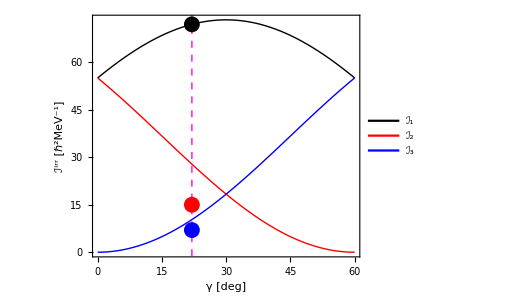

```mathematica
RIGIDPLOT=Plot[{rigidMOI[I0rig,1,betaExp,x],rigidMOI[I0rig,2,betaExp,x],rigidMOI[I0rig,3,betaExp,x]},{x,0,60},AspectRatio->0.8,ImageSize->380,Frame->True,Axes->False,FrameStyle->Directive[Black],PlotStyle->{{Black,Thick},{Red,Thick},{Blue,Thick}},FrameLabel->{"γ [deg]","ℐ^rig [ℏ^2MeV^-1]"},PlotLegends->Placed[{"ℐ_1","ℐ_2","ℐ_3"},{0.12,0.35}],LabelStyle->texStyle,Epilog->{Inset[Graphics[{Text[Style["γ=22^o",texStyle,Magenta]]}],Scaled[{0.5,0.7}]]}];
gfx1=Show[{RIGIDPLOT,Graphics[{Dashed,Thick,Magenta,Line[{{gamma,-10},{gamma,100}}]}],Graphics[{PointSize[0.03],Black,Point[{gamma,moisW2[[1]]}]}],Graphics[{PointSize[0.03],Red,Point[{gamma,moisW2[[2]]}]}],Graphics[{PointSize[0.03],Blue,Point[{gamma,moisW2[[3]]}]}]}];
HYDROPLOT=Plot[{hydroMOI[I0hyd,1,x],hydroMOI[I0hyd,2,x],hydroMOI[I0hyd,3,x]},{x,0,60},AspectRatio->0.8,ImageSize->380,Frame->True,Axes->False,FrameStyle->Directive[Black],PlotStyle->{{Black,Thick},{Red,Thick},{Blue,Thick}},FrameLabel->{"γ [deg]","ℐ^irr [ℏ^2MeV^-1]"},PlotLegends->Placed[{"ℐ_1","ℐ_2","ℐ_3"},{0.12,0.35}],LabelStyle->texStyle,Epilog->{Inset[Graphics[{Text[Style["γ=22^o",texStyle,Magenta]]}],Scaled[{0.5,0.7}]]}];
gfx2=Show[{HYDROPLOT,Graphics[{Dashed,Thick,Magenta,Line[{{gamma,-10},{gamma,100}}]}],Graphics[{PointSize[0.03],Black,Point[{gamma,moisW2[[1]]}]}],Graphics[{PointSize[0.03],Red,Point[{gamma,moisW2[[2]]}]}],Graphics[{PointSize[0.03],Blue,Point[{gamma,moisW2[[3]]}]}]}];
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Moments-Of-Inertia/rigid-mois-fit.pdf",gfx1,ImageResolution->1200];
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Moments-Of-Inertia/hydrodynamic-mois-fit.pdf",gfx2,ImageResolution->1200];
gfx1
gfx2
```